```mathematica
Get["sac.m",Path->NotebookDirectory[]];
```

```mathematica
?sac`*
```

```mathematica
history=Simulate[500,50000];
```

```mathematica
effectiveHistory=Take[history,-4000];
```

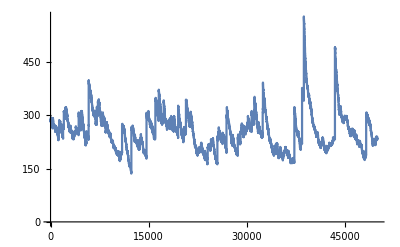

```mathematica
ListPlot[Unemployed[effectiveHistory],Joined->True,PlotRange->All]
```

```mathematica
firmHistories=FirmHistories[effectiveHistory];
```

```mathematica
firmProfitRates=FirmProfitRates[firmHistories];
```

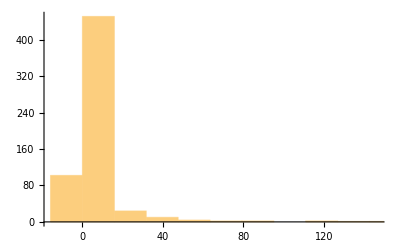
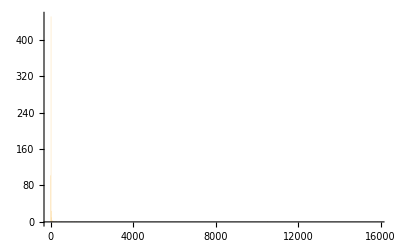

```mathematica
{Histogram[firmProfitRates],Histogram[firmProfitRates,PlotRange->All]}
```

```mathematica
firmSizes=FirmSizes[effectiveHistory];
```

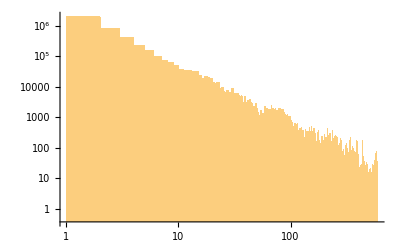

```mathematica
(* Should be a straight line *)
Histogram[firmSizes,PlotRange->All,ScalingFunctions->{"Log","Log"}]
```

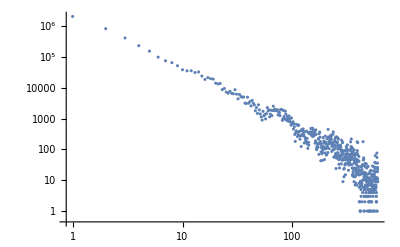

```mathematica
(* Should be a straight line *)
ListPlot[Drop[BinCounts[firmSizes],1],ScalingFunctions->{"Log","Log"},PlotRange->All]
```

```mathematica
EstimatedDistribution[firmSizes,ZipfDistribution[a,b]]
```

ZipfDistribution[597,0.713052]

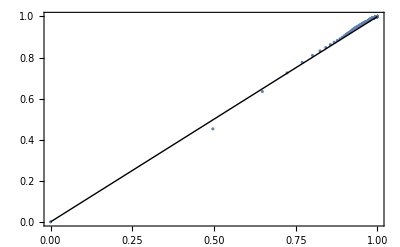

```mathematica
ProbabilityPlot[firmSizes,ZipfDistribution[a,b],PlotRange->All]
```

```mathematica
employeesMoney=EmployeesMoney[effectiveHistory];
```

$Aborted

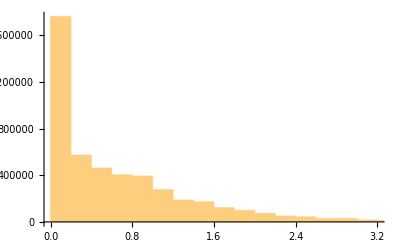

```mathematica
Histogram[employeesMoney]
```

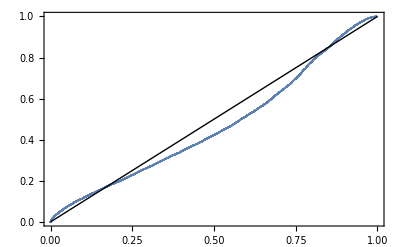

```mathematica
ProbabilityPlot[employeesMoney,GammaDistribution[a,b]]
```

```mathematica
employeesWealth=EmployeesWealth[effectiveHistory];
```

```mathematica
Histogram[employeesWealth]
```

-Graphics-

```mathematica
FindDistribution[employeesWealth,TargetFunctions->"Continuous",MaxItems->1,PerformanceGoal->"Quality"]
```

GammaDistribution[0.446314,1.39151]

```mathematica
ProbabilityPlot[employeesWealth,GammaDistribution[a,b]]
```

-Graphics-

```mathematica
employersWealth=EmployersWealth[effectiveHistory];
```

```mathematica
(* N.B. c=0 means location parameter is inoperative, and so reduces to ParetoDistribution[a,b] *)
EstimatedDistribution[employersWealth,ParetoDistribution[a,b,d]]
```

ParetoDistribution[5.62521,1.01925,0.000143897]

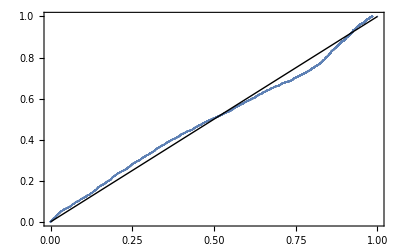

```mathematica
ProbabilityPlot[employersWealth,ParetoDistribution[a,b,d]]
```